setup the system of equations for the no-treatment model.

```mathematica
healthy={
k*A*(1-A/M1),
k*A*(A/M1)*(1-B/M2)-n*B,
q*H*(1-H/M3)
}
```

{A k (1-A/M1),(A^2 k (1-B/M2))/M1-B n,H (1-H/M3) q}

find the equilibria of the no-treatment model by setting each DE equal to zero.

```mathematica
healthyeq = Solve[healthy=={0,0,0},{A,B,H}]
```

{{A→0,B→0,H→0},{A→0,B→0,H→M3},{A→M1,B→(k M1 M2)/(k M1+M2 n),H→0},{A→M1,B→(k M1 M2)/(k M1+M2 n),H→M3}}

symbolically solve the Jacobian matrix of the system.

```mathematica
jacobian=D[healthy,{{A,B,H}}]
```

{{k (1-A/M1)-(A k)/M1,0,0},{(2 A k (1-B/M2))/M1,-(A^2 k)/(M1 M2)-n,0},{0,0,(1-H/M3) q-(H q)/M3}}

evaluate the jacobian at the first eq. and find its eigenvalues/vectors

```mathematica
firstj=jacobian/.{A->0,B->0,H->0}
firste=Eigensystem[firstj]
```

{{k,0,0},{0,-n,0},{0,0,q}}

{{k,-n,q},{{1,0,0},{0,1,0},{0,0,1}}}

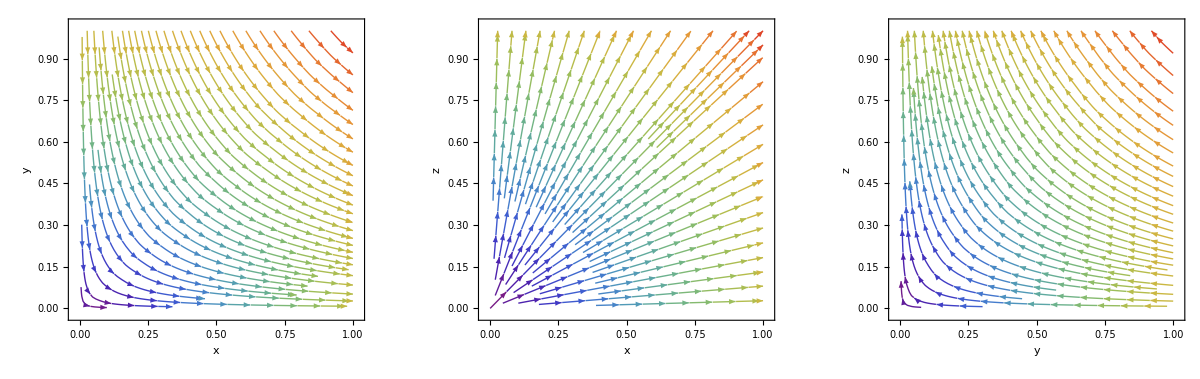

```mathematica
s1=StreamPlot[{x,-y},{x,0,1},{y,0,1},StreamColorFunction->"Rainbow",Axes->True,FrameLabel->{"x","y"}];
s2=StreamPlot[{x,z},{x,0,1},{z,0,1},StreamColorFunction->"Rainbow",Axes->True,FrameLabel->{"x","z"}];
s3=StreamPlot[{-y,z},{y,0,1},{z,0,1},StreamColorFunction->"Rainbow",Axes->True,FrameLabel->{"y","z"}];
p1=StreamPlot[{x,-y},{x,0,1},{y,0,1},StreamColorFunction->"Rainbow",Axes->True,FrameLabel->{"x","y"}];
Show[GraphicsGrid[{{"origin",s1,s2,s3}}],ImageSize->Full]
```

```mathematica
(*Table[StreamPlot[{p,q},{x,0,1},{y,0,1},StreamColorFunction->"Rainbow",Axes->True],{p,{x,x,-x}},{q,{-y,y,y}}]*)
```

The first equilibrium point is unstable since ∃λ > 0

evaluate the jacobian at the second eq. and find its eigenvalues/vectors

```mathematica
secondj=jacobian/.healthyeq[[2]]
seconde=Eigensystem[jacobian/.healthyeq[[2]]]
```

{{k,0,0},{0,-n,0},{0,0,-q}}

{{k,-n,-q},{{1,0,0},{0,1,0},{0,0,1}}}

The second equilibrium point is unstable since ∃λ > 0

evaluate the jacobian at the third eq. and find its eigenvalues/vectors

```mathematica
thirdj=jacobian/.healthyeq[[3]]
thirde=Eigensystem[jacobian/.healthyeq[[3]]]
```

{{-k,0,0},{2 k (1-(k M1)/(k M1+M2 n)),-(k M1)/M2-n,0},{0,0,q}}

{{-k,-(k M1+M2 n)/M2,q},{{-1/2+M1/M2+(k M1^2)/(2 M2^2 n)-(k M1)/(2 M2 n)+n/(2 k),1,0},{0,1,0},{0,0,1}}}

The third equilibrium point is unstable since ∃λ > 0

evaluate the jacobian at the fourth eq. and find its eigenvalues/vectors

```mathematica
fourthj=jacobian/.healthyeq[[4]]
fourthe=Eigensystem[jacobian/.healthyeq[[4]]]
```

{{-k,0,0},{2 k (1-(k M1)/(k M1+M2 n)),-(k M1)/M2-n,0},{0,0,-q}}

{{-k,-(k M1+M2 n)/M2,-q},{{-1/2+M1/M2+(k M1^2)/(2 M2^2 n)-(k M1)/(2 M2 n)+n/(2 k),1,0},{0,1,0},{0,0,1}}}

The fourth equilibrium point is asymptotically stable since all λ < 0.

```mathematica
Solve[0.26==s*D/k,D]
```

{{D→(0.26 k)/s}}